```mathematica
Exit[]
```

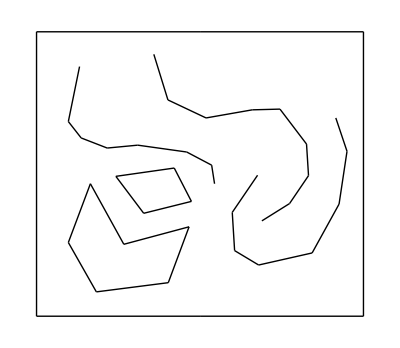

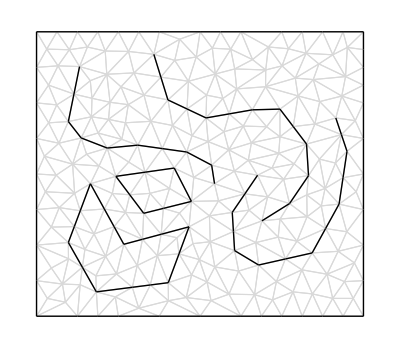

```mathematica
Needs["TriangleLink`"];

SetDirectory[NotebookDirectory[]];
svg=Import["in.svg","XML"];

(* some helper functions *)
getAttribute[tag_,attribute_]:=attribute/.tag⟦2⟧;
parsePoints[s_]:=ToExpression[StringSplit[StringSplit[s," "],","]];
ListAccumulate[l_]:=Module[{i,n,a},
a=l⟦1⟧;
n=Max[a];
For[i=2,i≤Length[l],i++,
a=Join[a,n+l⟦i⟧];
n+=Max[l⟦i⟧];
];
Return[a]
];

(* Constrained Delaunay triangulation with sizing h *)
Triangulate[points_,segments_,h_]:= Module[{T0,T},
T0=TriangleCreate[];
TriangleSetPoints[T0, points];
TriangleSetSegments[T0,segments];
T=TriangleTriangulate[T0,"pqa"<>ToString[h]];
Return[{
TriangleGetPoints[T],
TriangleGetElements[T],
TriangleGetSegments[T]
}];
];

(* extract polygons and polylines *)
polylines=Cases[svg,XMLElement["polyline",_,_],Infinity];
polygons=Cases[svg,XMLElement["polygon",_,_],Infinity];

(* build list of points *)
polylinePoints=parsePoints[getAttribute[#,"points"]]&/@polylines;
polygonPoints=parsePoints[getAttribute[#,"points"]]&/@polygons;
points=ArrayFlatten[Join[
polylinePoints,
polygonPoints
],1];

(* build list of segments *)
pathSegments[P_]:=Table[{i,i+1},{i,1,Length[P]-1}];
loopSegments[P_]:=Table[1+{i,Mod[i+1,Length[P]]},{i,0,Length[P]-1}];
segments=Join[
pathSegments/@polylinePoints,
loopSegments/@polygonPoints
];
segments=ListAccumulate[segments];

(* triangulate *)
{vertices,triangles,edges}=Triangulate[points,segments,100.0];

(* show input points and segments *)
Graphics[{GraphicsComplex[points,Line/@segments]}]

(* show output triangulation *)
Graphics[{FaceForm[],EdgeForm[LightGray],GraphicsComplex[vertices,Polygon/@triangles],Thick,Black,GraphicsComplex[vertices,Line/@edges]}]
```

```mathematica
(* Write mesh and curves to OBJ *)
SetDirectory[NotebookDirectory[]];
out=OpenWrite["out.obj"];

(* Write vertices *)
For[i=1,i≤Length[vertices],i++,
WriteString[out,"v"];
vi=Append[vertices⟦i⟧,0]; (* place in XY plane (Z=0) *)
For[p=1,p≤3,p++,
WriteString[out," "<>ToString[CForm[vi⟦p⟧]]];
];
WriteString[out,"\n"];
]

(* Write triangles *)
For[i=1,i≤Length[triangles],i++,
WriteString[out,"f"];
For[p=1,p≤3,p++,
WriteString[out," "<>ToString[triangles⟦i,p⟧]];
];
WriteString[out,"\n"];
];

(* Write segments *)
For[i=1,i≤Length[edges],i++,
WriteString[out,"l"];
For[p=1,p≤2,p++,
WriteString[out," "<>ToString[edges⟦i,p⟧]];
];
WriteString[out,"\n"];
];

Close[out];
```